Electron–positron cascades in multiple-laser optical traps

Marija Vranic, Thomas Grismayer, Ricardo A Fonseca and Luis O Silva, Plasma Phys. Control. Fusion 59 014040 (2017)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Figure 2

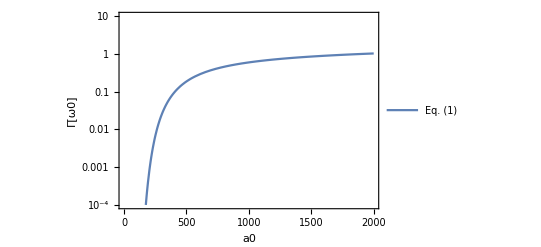

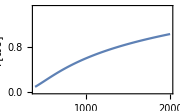

```mathematica
Clear[γavg,χavg,a0,aS,τc,ℏ,m,c,α,e,Γ,ω0]

(* physical constants and derived quantities*)
e=1.6 10^-19;
m=9.1 10^-31;
c=3 10^8;
ℏ=1.054571817 10^-34;
ϵ0=8.854 10^-12;
(**)
α=e^2/(2 ϵ0 2π ℏ c);(*~1/137 fine-structure constant, the paper uses units in which ϵ0 is not explicit *)
τc=ℏ/(m c^2); (* Compton wavelength *)

(* parameters *)
λ=0.8 10^-6;
ω0=2π c/λ;
aS=m c^2/(ℏ ω0);(* normalized vector potential of the Schwinger-Sauter field *)
γavg=6 a0; (* see text before eq 2 *)
χavg=12a0^2/(π aS); (* see text right after eq 2 *)


(* equation 1 *)
Γ=8/(15π)((2π)/3)^0.25 α/(τc γavg)BesselK[1/3,4/(3χavg)]^2;

(* main plot *)
LogPlot[Γ/ω0//Quiet,{a0,0,2000},Frame->True,FrameLabel->{"a0","Γ[ω0]"},PlotRange->{10^-4,10^1},PlotLegends->{"Eq. (1)"}]
(* inset *)
Plot[Γ/ω0//Quiet,{a0,400,2000},Frame->True,FrameLabel->{"a0","Γ[ω0]"},PlotRange->{10^-4,1.5},ImageSize->Small]
```

## Figure 4

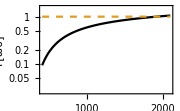

```mathematica
Clear[γavg,χavg,a0,aS,τc,ℏ,m,c,α,e,Γ,ω0]

(* physical constants and derived quantities*)
e=1.6 10^-19;
m=9.1 10^-31;
c=3 10^8;
ℏ=1.054571817 10^-34;
ϵ0=8.854 10^-12;
(**)
α=e^2/(2 ϵ0 2π ℏ c);(*~1/137 fine-structure constant, the paper uses units in which ϵ0 is not explicit *)
τc=ℏ/(m c^2); (* Compton wavelength *)

(* parameters *)
λ=0.8 10^-6;
ω0=2π c/λ;
aS=m c^2/(ℏ ω0);(* normalized vector potential of the Schwinger-Sauter field *)
γavg=6 a0; (* see text before eq 2 *)
χavg=12a0^2/(π aS); (* see text right after eq 2 *)

(* equation 1 *)
Γ=8/(15π)((2π)/3)^0.25 α/(τc γavg)BesselK[1/3,4/(3χavg)]^2;

(* main plot *)
LogPlot[{Γ/ω0//Quiet,1},{a0,400,2100},Frame->True,FrameLabel->{"a0","Γ[ω0]"},PlotRange->{10^-1.6,10^0.2},PlotLegends->{"Eq. (1)"},ImageSize->Small,PlotStyle->{Black,Dashed}]
```

## Appendix: Standing wave: 2 pulses, propagating in x-direction, polarized in z-direction

```mathematica
(* confirm with text after (A.1) and before (A.2) *)
Clear[a0,k0,ω0,x,t,ap,am]
ap={0,0,a0 Cos[k0 x - ω0 t]};
am={0,0,a0 Cos[k0 x + ω0 t]};

(* E: only z component *)
Ε=-D[ap+am,t]//Simplify
(* B: only y component *)
Β=Curl[ap+am,{x,y,z}]//Simplify
```

{0,0,2 a0 ω0 Cos[k0 x] Sin[t ω0]}

{0,2 a0 k0 Cos[t ω0] Sin[k0 x],0}

## Setup A

{0,0,2 a0 ω0 (Cos[k0 x]+Cos[k0 y]) Sin[t ω0]}

{-2 a0 k0 Cos[t ω0] Sin[k0 y],2 a0 k0 Cos[t ω0] Sin[k0 x],0}

-1/2 (Cos[k0 x]+Cos[k0 y])^2 (-2+Cos[2 k0 x]+Cos[2 k0 y])

1

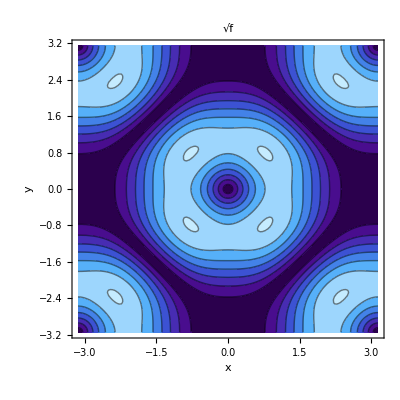

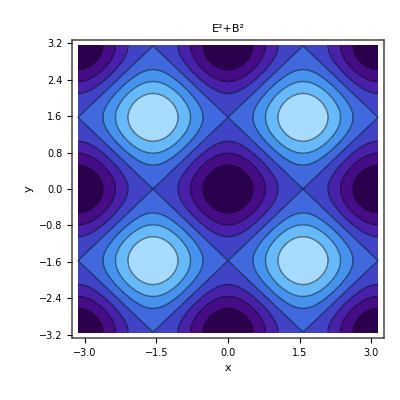

```mathematica
Clear[a0,k0,ω0,x,y,z,t,a1,a2,a3,a4,ΕxΒ2,fxy,Ε,Β,xmax]
a1={0,0,a0 Cos[k0 x - ω0 t]};
a2={0,0,a0 Cos[k0 x + ω0 t]};
a3={0,0,a0 Cos[k0 y - ω0 t]};
a4={0,0,a0 Cos[k0 y + ω0 t]};

(* E: only z component *)
Ε=-D[a1+a2+a3+a4,t]//Simplify
(* B: x and y components *)
Β=Curl[a1+a2+a3+a4,{x,y,z}]//Simplify

ΕxΒ2=Refine[Norm[Cross[Ε,Β]]^2//Simplify,{ω0>0,k0>0,a0>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 y] Sin[2 t ω0]>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 x] Sin[2 t ω0]>0}]//Simplify;
fxy=(Refine[Sqrt[ΕxΒ2]/(4a0^2 ω0 k0 Sin[ω0 t] Cos[ω0 t])//Simplify,{ω0>0,k0>0,a0>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 y] Sin[2 t ω0]>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 x] Sin[2 t ω0]>0,t ω0>0,Sin[2 t ω0]>0,Cos[k0 x]+Cos[k0 y]>0}]//Simplify)^2//Simplify
(* confirm with equation 4 *)
fxy/((Cos[k0 x]+Cos[k0 y])^2(Sin[k0 x]^2+Sin[k0 y]^2) )//Simplify

(* plotting parameters *)
t=0;k0=1;a0=1;
xmax=π;

ContourPlot[Sqrt[fxy],{x,-xmax,+xmax},{y,-xmax,+xmax},ColorFunction->"DeepSeaColors",PlotPoints->20,Frame->True,FrameLabel->{"x","y"},PlotLabel->"√f"]
ContourPlot[(Norm[Ε]^2+Norm[Β]^2),{x,-xmax,+xmax},{y,-xmax,+xmax},ColorFunction->"DeepSeaColors",PlotPoints->20,Frame->True,FrameLabel->{"x","y"},PlotLabel->"Ε^2+Β^2"]
```

## Setup B

{2 a0 ω0 Cos[k0 y] Sin[t ω0],2 a0 ω0 Cos[k0 x] Sin[t ω0],0}

{0,0,2 a0 k0 Cos[t ω0] (-Sin[k0 x]+Sin[k0 y])}

1/2 Abs[Sin[k0 x]-Sin[k0 y]]^2 (2+Cos[2 k0 x]+Cos[2 k0 y])

1

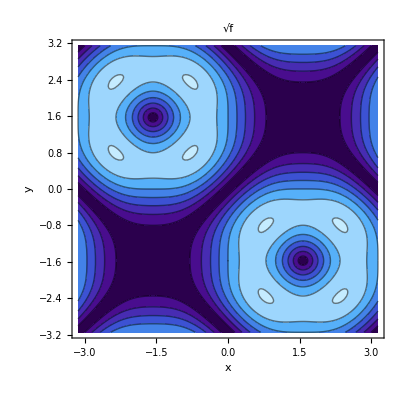

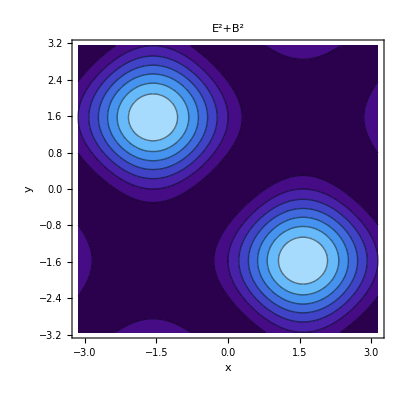

```mathematica
Clear[a0,k0,ω0,x,y,z,t,a1,a2,a3,a4,ΕxΒ2,fxy,Ε,Β,xmax]
a1={0,a0 Cos[k0 x - ω0 t],0};
a2={0,a0 Cos[k0 x + ω0 t],0};
a3={a0 Cos[k0 y - ω0 t],0,0};
a4={a0 Cos[k0 y + ω0 t],0,0};

(* E: x and y components *)
Ε=-D[a1+a2+a3+a4,t]//Simplify
(* B: only z component *)
Β=Curl[a1+a2+a3+a4,{x,y,z}]//Simplify

ΕxΒ2=Refine[Norm[Cross[Ε,Β]]^2//Simplify,{ω0>0,k0>0,a0>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 y] Sin[2 t ω0]>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 x] Sin[2 t ω0]>0}]//Simplify;
fxy=(Refine[Sqrt[ΕxΒ2]/(4a0^2 ω0 k0 Sin[ω0 t] Cos[ω0 t])//Simplify,{ω0>0,k0>0,a0>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 y] Sin[2 t ω0]>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 x] Sin[2 t ω0]>0,t ω0>0,Sin[2 t ω0]>0,Cos[k0 x]+Cos[k0 y]>0}]//Simplify)^2//Simplify
(* confirm with equation 5 *)
Refine[fxy/((Cos[k0 x]^2+Cos[k0 y]^2)(Sin[k0 x]-Sin[k0 y])^2 )//Simplify,{Sin[k0 x]-Sin[k0 y]>0}]

(* plotting parameters *)
t=0;k0=1;a0=1;
xmax=π;

ContourPlot[Sqrt[fxy],{x,-xmax,+xmax},{y,-xmax,+xmax},ColorFunction->"DeepSeaColors",PlotPoints->20,Frame->True,FrameLabel->{"x","y"},PlotLabel->"√f"]
ContourPlot[(Norm[Ε]^2+Norm[Β]^2),{x,-xmax,+xmax},{y,-xmax,+xmax},ColorFunction->"DeepSeaColors",PlotPoints->20,Frame->True,FrameLabel->{"x","y"},PlotLabel->"Ε^2+Β^2"]
```

## Setup C

{0,2 a0 ω0 Cos[k0 x] Sin[t ω0],2 a0 ω0 Cos[k0 y] Sin[t ω0]}

{-2 a0 k0 Cos[t ω0] Sin[k0 y],0,-2 a0 k0 Cos[t ω0] Sin[k0 x]}

1/4 (Sin[2 k0 x]^2+2 (2+Cos[2 k0 x]+Cos[2 k0 y]) Sin[k0 y]^2)

1

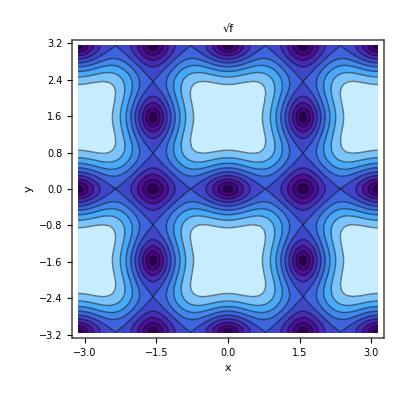

-Graphics-

```mathematica
Clear[a0,k0,ω0,x,y,z,t,a1,a2,a3,a4,ΕxΒ2,fxy,Ε,Β,xmax]
a1={0,a0 Cos[k0 x - ω0 t],0};
a2={0,a0 Cos[k0 x + ω0 t],0};
a3={0,0,a0 Cos[k0 y - ω0 t]};
a4={0,0,a0 Cos[k0 y + ω0 t]};

(* E: y and z components *)
Ε=-D[a1+a2+a3+a4,t]//Simplify
(* B: x and z components *)
Β=Curl[a1+a2+a3+a4,{x,y,z}]//Simplify

ΕxΒ2=Refine[Norm[Cross[Ε,Β]]^2//Simplify,{ω0>0,k0>0,a0>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 y] Sin[2 t ω0]>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 x] Sin[2 t ω0]>0}]//Simplify;
fxy=(Refine[Sqrt[ΕxΒ2]/(4a0^2 ω0 k0 Sin[ω0 t] Cos[ω0 t])//Simplify,{ω0>0,k0>0,a0>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 y] Sin[2 t ω0]>0,(Cos[k0 x]+Cos[k0 y]) Sin[k0 x] Sin[2 t ω0]>0,t ω0>0,Sin[2 t ω0]>0,Cos[k0 x]+Cos[k0 y]>0,Sin[2 k0 x]>0,Sin[2 k0 y]>0}]//Simplify)^2//FullSimplify

(* confirm with equation 6 *)
Refine[fxy/(Sin[k0 x]^2 Cos[k0 x]^2+Sin[k0 y]^2 Cos[k0 y]^2+Cos[k0 x]^2 Sin[k0 y]^2)//Simplify,{Sin[2 k0 x]>0,Sin[2 k0 y]>0}]//FullSimplify

(* plotting parameters *)
t=0;k0=1;a0=1;
xmax=π;

ContourPlot[Sqrt[fxy],{x,-xmax,+xmax},{y,-xmax,+xmax},ColorFunction->"DeepSeaColors",PlotPoints->20,Frame->True,FrameLabel->{"x","y"},PlotLabel->"√f"]
ContourPlot[(Norm[Ε]^2+Norm[Β]^2),{x,-xmax,+xmax},{y,-xmax,+xmax},ColorFunction->"DeepSeaColors",PlotPoints->20,Frame->True,FrameLabel->{"x","y"},PlotLabel->"Ε^2+Β^2"]
```

```mathematica
(* spatial averages *)
Clear[t,k0,a0,x,y,xmax,fA,fB,fC,fAavg,fBavg,fCavg]
t=0;k0=1;a0=1;
xmax=π;

fA=(Cos[k0 x]+Cos[k0 y])^2(Sin[k0 x]^2+Sin[k0 y]^2);
fB=(Cos[k0 x]^2+Cos[k0 y]^2)(Sin[k0 x]-Sin[k0 y])^2 ;
fC=Sin[k0 x]^2 Cos[k0 x]^2+Sin[k0 y]^2 Cos[k0 y]^2+Cos[k0 x]^2 Sin[k0 y]^2;

fAavg=NIntegrate[Sqrt[fA],{x,-xmax,+xmax},{y,-xmax,+xmax}]/NIntegrate[1,{x,-xmax,+xmax},{y,-xmax,+xmax}]//Quiet

fBavg=NIntegrate[Sqrt[fB],{x,-xmax,+xmax},{y,-xmax,+xmax}]/NIntegrate[1,{x,-xmax,+xmax},{y,-xmax,+xmax}]//Quiet

fCavg=NIntegrate[Sqrt[fC],{x,-xmax,+xmax},{y,-xmax,+xmax}]/NIntegrate[1,{x,-xmax,+xmax},{y,-xmax,+xmax}]//Quiet

fAavg/fCavg
0.9/0.8

(* "It is, therefore, expected that χe^- is on the same order for all the configurations A–C" *)
```

0.730708

0.730708

0.665408

1.09813

1.125